```mathematica
(**********************************************************************************)
```

```mathematica
Clear["Global`*"]
```

```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
inputfile=OpenRead["background.txt"]
```

InputStream[…]

```mathematica
data=ReadList[inputfile,{Number,Number,Number,Number,Number,Number,Number,Number}];
```

```mathematica
Close[inputfile]
```

background.txt

```mathematica
ndata=Length[data]
```

11514

```mathematica
tablea=Table[data[[i,1]],{i,1,ndata}];
```

```mathematica
tableHt=Table[data[[i,2]],{i,1,ndata}];
```

```mathematica
tablephit=Table[data[[i,3]],{i,1,ndata}];
```

```mathematica
tablephitp=Table[data[[i,4]],{i,1,ndata}];
```

```mathematica
tablechit=Table[data[[i,5]],{i,1,ndata}];
```

```mathematica
tablechitp=Table[data[[i,6]],{i,1,ndata}];
```

```mathematica
tablesigmat=Table[data[[i,7]],{i,1,ndata}];
```

```mathematica
tablesigmatp=Table[data[[i,8]],{i,1,ndata}];
```

```mathematica
amin=tablea[[1]]
```

0.00001

```mathematica
amax=tablea[[ndata]]
```

1.

```mathematica
tableaHt=Table[{tablea[[i]],tableHt[[i]]},{i,1,ndata}];
```

```mathematica
tableaphit=Table[{tablea[[i]],tablephit[[i]]},{i,1,ndata}];
```

```mathematica
tableaphitp=Table[{tablea[[i]],tablephitp[[i]]},{i,1,ndata}];
```

```mathematica
tableachit=Table[{tablea[[i]],tablechit[[i]]},{i,1,ndata}];
```

```mathematica
tableachitp=Table[{tablea[[i]],tablechitp[[i]]},{i,1,ndata}];
```

```mathematica
tableasigmat=Table[{tablea[[i]],tablesigmat[[i]]},{i,1,ndata}];
```

```mathematica
tableasigmatp=Table[{tablea[[i]],tablesigmatp[[i]]},{i,1,ndata}];
```

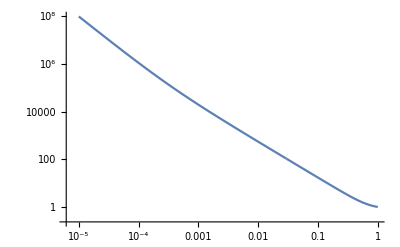

```mathematica
ListLogLogPlot[tableaHt,Joined->True]
```

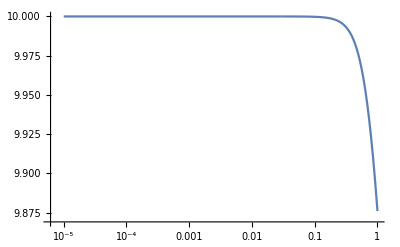

```mathematica
ListLogLinearPlot[tableaphit,Joined->True,PlotRange->All]
```

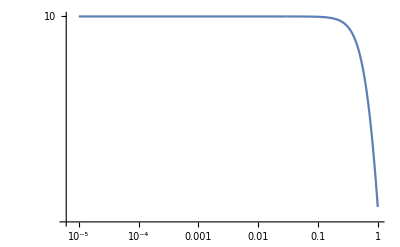

```mathematica
ListLogLogPlot[tableaphit,Joined->True,PlotRange->All]
```

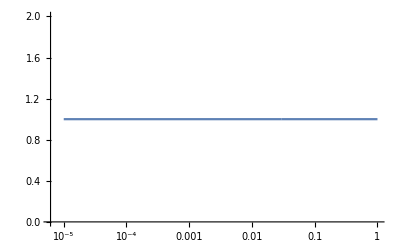

```mathematica
ListLogLinearPlot[tableachit,Joined->True,PlotRange->All]
```

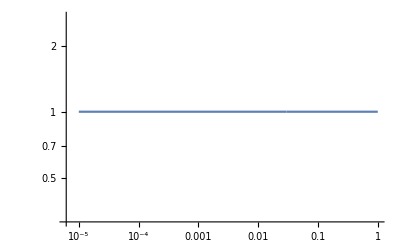

```mathematica
ListLogLogPlot[tableachit,Joined->True,PlotRange->All]
```

```mathematica
ListLogLinearPlot[tableasigmat,Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListLogLogPlot[tableasigmat,Joined->True,PlotRange->All]
```

-Graphics-

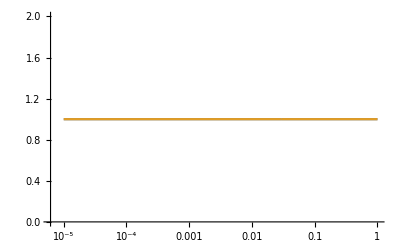

```mathematica
ListLogLinearPlot[{tableachit,tableasigmat},Joined->True,PlotRange->All]
```

```mathematica
(**********************************************************************************)
```